```mathematica
FetchData[filename_]:=  Import[NotebookDirectory[]<>"../data/simulation/"<>filename];
ExportData[filename_, data_]:= Export[NotebookDirectory[]<>"../data/simulation/"<>filename, data];
```

## Building (stationary) adjacency graph

```mathematica
db = DatabaseReference[FindFile[NotebookDirectory[]<>"/../data/genova.db"]]

(* We select the absolute, treat F and T roads as the same. This simplifies graph and reduces computation time. Since data is bad anyways, I don't think this will affect the results by much.*)
queryGraphLinks = ExternalEvaluate[db, "
	WITH e(edge_id, node_from_id, node_to_id) AS (
		SELECT geo_edges.edge_id, geo_edges.node_from_id, geo_edges.node_to_id
		FROM geo_edges
		
	), g(edge_id, node_from_id, node_to_id) AS (
		SELECT geo_edges.edge_id, geo_edges.node_from_id, geo_edges.node_to_id
		FROM geo_edges
		
	)
	SELECT ABS(g.edge_id) as \"from\", ABS(e.edge_id) AS \"to\"
	FROM e
	INNER JOIN g
	WHERE e.node_to_id = g.node_from_id AND ABS(g.edge_id) <> ABS(e.edge_id)
	UNION
	SELECT ABS(e.edge_id) AS \"from\", ABS(g.edge_id) as \"to\"
	FROM e
	INNER JOIN geo_edges g
	WHERE e.node_from_id = g.node_to_id AND ABS(g.edge_id) <> ABS(e.edge_id)
;"];

(* We select max because we are interested on the study of the congested direction of the road*)
queryTrafficData = ExternalEvaluate[db, "
	SELECT
		g.edge_id AS edge_id,
		MAX(t.count_mean) AS count
	FROM geo_edges g
	INNER JOIN traffic_data t
	ON g.edge_id = ABS(t.edge_id)
	WHERE t.hour_slot = 170
	GROUP BY g.edge_id
;"];

graphLinks = Thread[#["from"]<-> #["to"] /. #]&/@Normal[queryGraphLinks];
g=SimpleGraph[graphLinks[[;;]],VertexLabels->None];
validNodes = queryTrafficData[[;;, 1]];
invalidNodes = Select[VertexList[g], !MemberQ[validNodes, #]&];
g = VertexDelete[g, invalidNodes];
disconnectedNodes = Flatten[ConnectedComponents[g][[2;;]]]; (* Remove disconnected train network *)
g = VertexDelete[g, disconnectedNodes];

ExportData["g.mx", g];
```

DatabaseReference[…]

## Getting parameters from data

### Get car counts

```mathematica
GetTrafficAtHour = (hour)↦ExternalEvaluate[db, "
	with tmp(edge_id, count) AS (
		SELECT g.edge_id AS edge_id,
		MAX(t.count_mean) AS count
		FROM geo_edges g
		INNER JOIN traffic_data t
		ON g.edge_id = ABS(t.edge_id)
		WHERE t.hour_slot = "<>ToString[hour]<>"
		GROUP BY g.edge_id
	)
	SELECT tmp.edge_id, tmp.count/(SELECT SUM(tmp.count) FROM tmp) AS fraction
	FROM tmp
	ORDER BY edge_id
;"]; (* TODO check ordering *)
```

### Get road geo position

```mathematica
BinarySearch = ResourceFunction["BinarySearch"];

GetRoadCoordinates = (g)↦Module[{edgeList, query,  queryIds, coordsPosition, data},
edgeList = VertexList@g;

query = ExternalEvaluate[db, "
		SELECT edge_id, AVG(lat) AS lat, AVG(lon) AS long
		FROM geo_nodes n
		INNER JOIN geo_edges e ON node_to_id = n.id OR node_from_id = n.id
		GROUP BY edge_id
		ORDER BY edge_id
	;"];

queryIds = Normal@query[[;;, 1]];
coordsPosition = ParallelMap[BinarySearch[queryIds, #] &, edgeList];

data = {Normal@query[[;;, 2]], Normal@query[[;;,3]]} // Transpose ;
ParallelMap[GeoPosition@data[[#]]&, coordsPosition]
];
```

### Speed

```mathematica
BinarySearch = ResourceFunction["BinarySearch"];

GetRoadSpeeds = (g)↦Module[{edgeList, query,  queryIds, speedPosition, data},
edgeList = VertexList@g;

query = ExternalEvaluate[db, "
		SELECT edge_id, speed
		FROM geo_edges
		ORDER BY edge_id
	;"];

queryIds = Normal@query[[;;, 1]];
speedPosition = ParallelMap[BinarySearch[queryIds, #] &, edgeList];

 data = Normal@query[[;;, 2]];

ParallelMap[data[[#]]&, speedPosition]
];
```

### Thresholds heuristics

```mathematica
BinarySearch = ResourceFunction["BinarySearch"];
 
averageCarLength = 3.5;

GetRoadThresholds = (g)↦Module[{query, edgeList, data, queryIds, thresholdPositions}, 
(* 3.5m is the average car length in italy *)
edgeList = VertexList@g; (*Vertices in the graph are edges in the db*)
 (*speed/50 approx nLanes*)
query = ExternalEvaluate[db, "
		SELECT edge_id, edge_length * speed / 50 / (speed/3.6*1 + "<>ToString@averageCarLength<>") as threshold
		FROM geo_edges
		ORDER BY edge_id
	;"];
queryIds = Normal@query[[;;, 1]];
thresholdPositions = ParallelMap[BinarySearch[queryIds, #] &, edgeList];

query[[#, 2]] &/@ thresholdPositions
];
```

### Flow heuristics

```mathematica
BinarySearch = ResourceFunction["BinarySearch"];
 
averageCarLength = 3.5;

GetRoadFlows = (g)↦Module[{query, edgeList, data, queryIds, flowsPositions}, 
(* 3.5m is the average car length in italy *)
edgeList = VertexList@g; (*Vertices in the graph are edges in the db*)
 (*speed/50 approx nLanes*)
query = ExternalEvaluate[db, "
		SELECT edge_id, speed / 50 / (speed/3.6*1 + "<>ToString@averageCarLength<>")*speed as max_flow
		FROM geo_edges
		ORDER BY edge_id
	;"];
queryIds = Normal@query[[;;, 1]];
flowsPositions = ParallelMap[BinarySearch[queryIds, #] &, edgeList];

query[[#, 2]] &/@ flowsPositions
];
```

### Stationary Probabilities

```mathematica
BinarySearch = ResourceFunction["BinarySearch"];

GetStatProbs = (g)↦Module[{query, edgeList, data, queryIds, thresholdPositions, cumulativeCounts}, 
edgeList = VertexList@g; (*Vertices in the graph are edges in the db*)

query = ExternalEvaluate[db, "
		SELECT g.edge_id, SUM(t.count_mean) as n
		FROM geo_edges g
		INNER JOIN traffic_data t
		ON g.edge_id = ABS(t.edge_id)
		WHERE (t.hour_slot BETWEEN 93 AND 101) OR (t.hour_slot BETWEEN 205 AND 222)
		GROUP BY g.edge_id
		ORDER BY g.edge_id
	;"];
queryIds = Normal@query[[;;, 1]];
thresholdPositions = ParallelMap[BinarySearch[queryIds, #] &, edgeList];

(*Avoid division by zero errors!*)
cumulativeCounts = 1+query[[#, 2]] &/@ thresholdPositions;
cumulativeCounts /= Total@cumulativeCounts
];
```

### Dijkstra

```mathematica
BinarySearch = ResourceFunction["BinarySearch"];

GetRoadTimes = (g)↦Module[{edgeList, query,  queryIds, timePosition, data},
edgeList = VertexList@g;

query = ExternalEvaluate[db, "
		SELECT edge_id, edge_length / speed * 3.6 as time
		FROM geo_edges
		ORDER BY edge_id
	;"];

queryIds = Normal@query[[;;, 1]];
timePosition = ParallelMap[BinarySearch[queryIds, #] &, edgeList];

 data = Normal@query[[;;, 2]];

ParallelMap[data[[#]]&, timePosition]
];
```

## Mobility demands

```mathematica
statProbs = GetStatProbs@g;
max = Length@statProbs;
probRatios = ParallelTable[Table[Sqrt[statProbs[[from]] / statProbs[[to]]], {from, 1, max}], {to, 1, max}];

MakeMarkov = (mat) ↦ # / Total@# &/@ ( probRatios mat);
```

### Demo

```mathematica
ClearAll["SampleMarkovMatrix"];
SampleMarkovMatrix[n_,min_:0]:=If[min n<1,Transpose@RandomPoint[Simplex[IdentityMatrix[n](1-min n)],n]+min,$Failed];

ClearAll["SampleThresholds"];
SampleThresholds = (n) ↦ Table[RandomInteger[{2, Floor@Sqrt@n}], n];
```

### Naive

```mathematica
A = AdjacencyMatrix@g;

ExportData["w-naive.mx", MakeMarkov@A];
```

### Speed-based

```mathematica
speeds = GetRoadSpeeds[g];
A = AdjacencyMatrix@g;
divideMap[num_, arr_] :=num/#&/@arr;
mobilityDemandSpeed = A ParallelMap[divideMap[#, speeds]&, speeds];

ExportData["w-speed.mx", MakeMarkov@mobilityDemandSpeed];
```

### Time-based

```mathematica
times = GetRoadTimes[g];
weights = #1->#2&@@@Transpose@{VertexList@g, times} ;
directedEdges = Flatten[{#1 -> #2, #2 ->#1} &@@@(EdgeList@g)[[;;, 1;;2]]];
edgeWeights = ParallelMap[(#/.weights)&, directedEdges[[;;, 2]]];
wg = Graph[directedEdges, EdgeWeight->edgeWeights];

hi = ParallelMap[GraphDistance[wg, #, 55260577]&, VertexList@g]; (*55260577 via antonio gramsci, 
davanti al sommergibile nazario sauro*)
hi /= Total[hi];
hi=If[#<.00002,.00002,#]&/@hi;

ExportData["h_i.mx", hi];
```

```mathematica
hi = FetchData["h_i.mx"];
hiInv = 1 / # &/@hi;

A = AdjacencyMatrix@g;
mobilityDemandTime = A Table[hiInv, VertexCount@g];

ExportData["w-time.mx", MakeMarkov@mobilityDemandTime];
```

## Thresholds and flows

```mathematica
ExportData["flows.mx", GetRoadFlows@g];
ExportData["thresholds.mx", GetRoadThresholds@g];
```

## Fundamental Diagram

```mathematica
GetSpeedAndDensityOfSingleRoad = (edgeId) ↦ Module[{queryNodeCapacity, fluxValues, densityValues},
queryNodeCapacity = ExternalEvaluate[db, "
		SELECT
			t.hour_slot as time, AVG(t.count_mean / g.edge_length) AS density, AVG(t.speed_mean)*AVG(t.count_mean / g.edge_length) AS flux
		FROM traffic_data t
		INNER JOIN geo_edges g
		ON g.edge_id = t.edge_id AND ABS(t.edge_id) = "<>ToString[edgeId]<>"
		GROUP BY t.hour_slot
	;"];
fluxValues = Normal@Transpose[queryNodeCapacity]["flux"];
densityValues = Normal@Transpose[queryNodeCapacity]["density"];

{densityValues, fluxValues} // Transpose
];

PlotCongestionOfSingleRoad = (edgeId) ↦ Module[{},
ListPlot[GetSpeedAndDensityOfSingleRoad[edgeId], PlotRange->All]
];
```

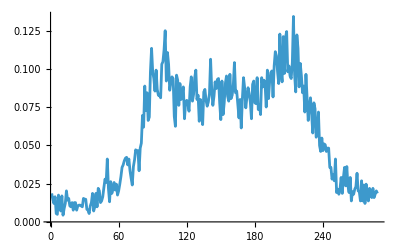

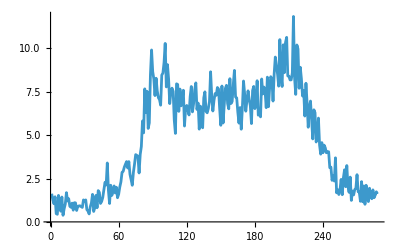

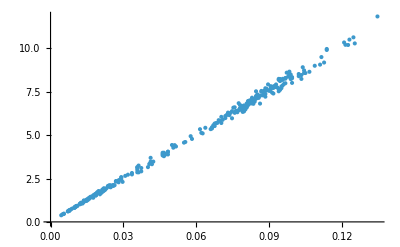

```mathematica
testRoad = GetSpeedAndDensityOfSingleRoad[55255453];
ListLinePlot[testRoad[[;;, 1]]]
ListLinePlot[testRoad[[;;, 2]]]
ListPlot[testRoad]
```

```mathematica
validNodes = VertexList[g];
$DefaultParallelKernels= {8};
CloseKernels[]
LaunchKernels[];
heatmapPoints = ParallelMap[GetSpeedAndDensityOfSingleRoad, validNodes, Method->"ItemsPerEvaluation" -> 10];
```

```mathematica
Export["heatmapPoints.mx", heatmapPoints];
```

```mathematica
heatmapPoints = Import["C:\\Users\\Matteo\\Documents\\heatmapPoints.mx"];
```

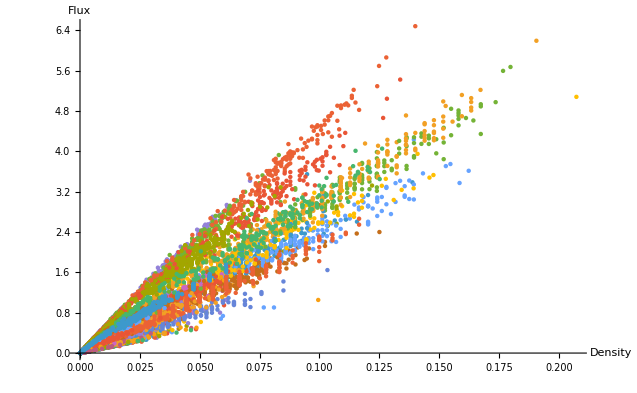

```mathematica
ListPlot[heatmapPoints[[200;;500]], AxesLabel->{"Density", "Flux"}, PlotStyle->PointSize[.005], PlotRange->Full]
```

### pocci

```mathematica
startTime = 80;
endTime = 83;
fractions = ParallelTable[Normal@GetTrafficAtHour[i][[;;100,2]], {i, startTime, endTime}];
```

```mathematica
M = VertexCount[g];
estimatedRates = EstimatedProcess[fractions,  DiscreteMarkovProcess[100]];
estimatedRates
```

```mathematica
EstimatedProcess[{{1, 1 ,1}, {2, 2, 2}, {3, 3, 3}, {1, 1, 1}}, DiscreteMarkovProcess[3]]
```

DiscreteMarkovProcess[{1/2,1/4,1/4},{{1,0,0},{0,1,0},{0,0,1}}]

```mathematica
𝒫=DiscreteMarkovProcess[3,{{1/2,1/2,0,0},{1/2,1/2,0,0},{1/4,1/4,1/4,1/4},{0,0,0,1}}];
p = StationaryDistribution[𝒫] // Normal
PDF[p, x]
```

ProbabilityDistribution[1/3 Boole[x==1]+1/3 Boole[x==2]+1/3 Boole[x==4],{x,1,4,1}]

Piecewise[{{1/3 Boole[x==1]+1/3 Boole[x==2]+1/3 Boole[x==4], 1≤x≤4}, {0, True}}]

```mathematica
{{1/2,1/2,0,0},{1/2,1/2,0,0},{1/4,1/4,1/4,1/4},{0,0,0,1}} // Eigenvectors
```

{{-1/2,-1/2,0,1},{3/2,3/2,1,0},{0,0,1,0},{-1,1,0,0}}

```mathematica
m = {{0, 1/3, 1/3},{1/2, 1/3, 1/3},{1/2, 1/3, 1/3}};
Eigenvalues[m]
Eigenvectors[m]
p = {0, -1, 1}
Norm[m.p] == 0
estim = {{a, b, c}, {d, e, f}, {g, h, i}};
eqns = {}
For[k=1, k<=3, k++, For[l = 1, l<=3, l++, AppendTo[eqns, estim[[k, l]]p[[k]] == estim[[l, k]]p[[l]]]]]
eqns
Solve[b==(2 d)/3&&c ==(2 g)/3 &&(2 d)/3==b && f==h &&(2 g)/3==c && a + d + g == 1 && b + e + h == 1 && c + f + i == 1] //N
```

```mathematica
$DefaultParallelKernels = {4}
CloseKernels[]
LaunchKernels[]
```

```mathematica
Mean[EstimatedProcess[data,Discere[n,n*n]][[2]]-markovMatrix//Flatten]
Variance[EstimatedProcess[data,HiddenMarkovProcess[n,n*n]][[2]]-markovMatrix//Flatten]
Mean[markovMatrix//Flatten]
Variance[markovMatrix//Flatten]
```

```mathematica
(*Pocci*)
proc = DiscreteMarkovProcess[statDist // Flatten, markovMatrix];
data = RandomFunction[proc, {0, 2}, agentCount];
Histogram[data]
```

```mathematica
GetTrafficAtHour[170]
```

Dataset[<>]

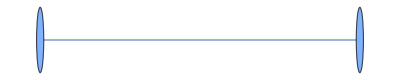

```mathematica
f = SimpleGraph[{1<->2, 2<->1, 1<->2}]
```

```mathematica
AdjacencyMatrix[f] // Normal
```

{{0,3},{3,0}}

SparseArray[<64640>, {18410, 18410}]